```mathematica
step = .00001;
diff[p_,q_]:=Which[#>.5,#-.5,#<-.5,#+.5,True,#]&/@(q-p);
shift[p_,q_]:=
If[Abs[#.#]>.001,step #/#.#,{0,0}]&@diff[p,q];
move[pt_,list_]:=Plus@@(shift[pt,#]&/@list)
movepts[list_]:=Mod[(#+move[#,list])&/@list,1]
SeedRandom[];
start = Table[{Random[],Random[]},400];
seq = NestList[movepts,start,20];
```

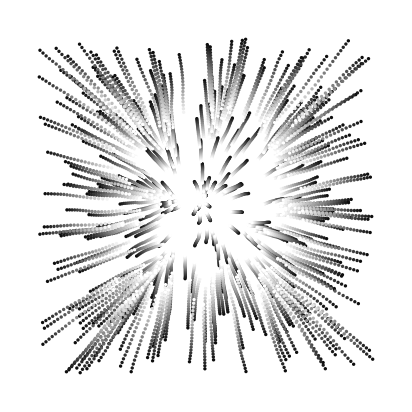

```mathematica
Graphics[Table[{GrayLevel[.05 k],Disk[#,.005]&/@seq[[k]]},{k,1,20}]]
```

```mathematica
Graphics[{Line[{{0,0},{0,1},{1,1},{1,0}}],Table[{GrayLevel[.4],Disk[#,.005]&/@seq[[k]]},{k,1,1}]}]
```

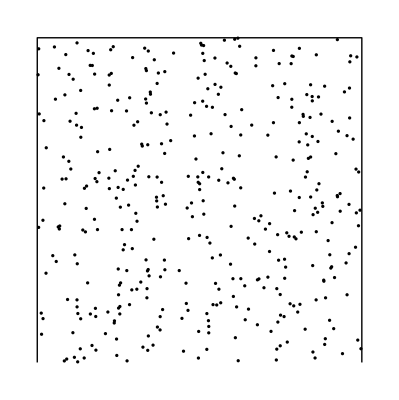

```mathematica
Graphics[{Line[{{0,0},{0,1},{1,1},{1,0}}],Disk[#,.005]&/@start}]
```

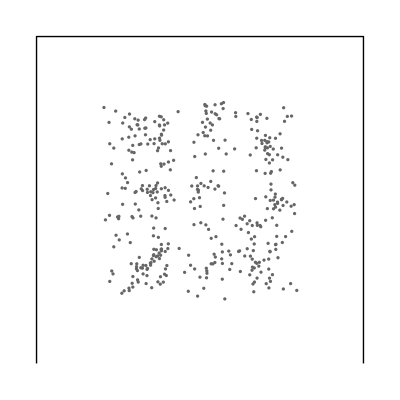

```mathematica
Graphics[{Line[{{0,0},{0,1},{1,1},{1,0}}],Table[{GrayLevel[.4],Disk[#,.005]&/@seq[[k]]},{k,20,20}]}]
```

```mathematica
diff[{.1,.7},{.9,.3}]
```

{0.3,-0.4}

```mathematica
N
```

```mathematica
tobinary[list_]:=Plus@@(Table[2^(k-1)list[[k]],{k,Length[list]}])
```

```mathematica
len = 3;

parse[list_]:=(parsed=Array[0&,2^len];Table[parsed[[1+tobinary[Take[Join[list,list],{k,k+len-1}]]]]++,{k,1,Length[list]}];parsed)
```

```mathematica
ll=Array[RandomChoice[{0,1}]&,128]
```

{1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,1,0,1,0,0,0,0,0,1,1,1,1,1,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,1,1,0,1,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1,1,1}

```mathematica
parse[ll]
```

{12,11,17,10,11,16,10,13}

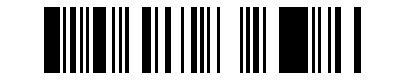

```mathematica
ArrayPlot[{ll}]
```

```mathematica
ll=Array[Floor[Sin[#/10]127+127]&,128]
```

{139,152,164,176,187,198,208,218,226,233,240,245,249,252,253,253,252,250,247,242,236,229,221,212,203,192,181,169,157,144,132,119,106,94,82,70,59,49,39,30,23,16,10,6,2,0,0,0,2,5,9,14,21,28,37,46,57,67,79,91,103,116,129,141,154,166,178,189,200,210,219,227,235,241,246,249,252,253,253,252,250,246,241,235,228,220,211,201,190,179,167,155,142,130,117,104,92,80,68,57,47,38,29,21,15,9,5,2,0,0,0,2,5,10,15,22,30,38,48,58,69,81,93,105,118,131,143,156}

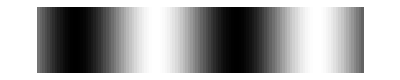

```mathematica
ArrayPlot[{ll}]
```

```mathematica
haardifferencesof[list_]:=Table[{(ll[[i]]+ll[[i+1]]),(ll[[i]]-ll[[i+1]])},{i,Length[list]/2}]
```

```mathematica
haardifferencesof[ll]
```

{{291,-13},{316,-12},{340,-12},{363,-11},{385,-11},{406,-10},{426,-10},{444,-8},{459,-7},{473,-7},{485,-5},{494,-4},{501,-3},{505,-1},{506,0},{505,1},{502,2},{497,3},{489,5},{478,6},{465,7},{450,8},{433,9},{415,9},{395,11},{373,11},{350,12},{326,12},{301,13},{276,12},{251,13},{225,13},{200,12},{176,12},{152,12},{129,11},{108,10},{88,10},{69,9},{53,7},{39,7},{26,6},{16,4},{8,4},{2,2},{0,0},{0,0},{2,-2},{7,-3},{14,-4},{23,-5},{35,-7},{49,-7},{65,-9},{83,-9},{103,-11},{124,-10},{146,-12},{170,-12},{194,-12},{219,-13},{245,-13},{270,-12},{295,-13}}